## Michael Reid' s Data from Crosswhite

```mathematica
Protect/@{M0,M2,M4,P2,P4,P6,F2,F4,F6,α,β,γ};
```

```mathematica
RemoveWhiteSpace[str_]:=(
Return[StringReplace[str,RegularExpression["\\s+"]->" "]];
);

RemoveAllWhite[str_]:=(
Return[StringReplace[str,RegularExpression["\\s"]->""]]
);

ParseCFPRow[row_]:=(
numChunks=Round[StringLength[row]/16];
pieces=Table[StringTake[row,{16*i+1,16*(i+1)}],{i,0,numChunks-1,1}];
Return[pieces]
);

ParseCFPRows[rows_]:=ParseCFPAtom/@Flatten[ParseCFPRow/@rows];
ParseCFPAtom[atom_]:={ToExpression[StringTake[atom,{1,4}]],
ToExpression[StringTake[atom,{5,16}]]};

BraKetRowParser[row_]:=(
bra=RemoveAllWhite[StringTake[row,{2,4}]];
ket=RemoveAllWhite[StringTake[row,{6,8}]];
nums=RemoveWhiteSpace[StringTake[row,{9,-1}]];
nums=ToExpression/@StringSplit[nums," "];
Return[{bra,ket,nums}]
);

SingleTermParser[row_]:=(
term=RemoveAllWhite[StringTake[row,{2,4}]];
nums=StringTake[row,{8,-1}];
nums=RemoveWhiteSpace[nums];
nums=ToExpression/@StringSplit[nums," "];
Return[{term,nums}]
);

OffDiagonalParser[row_]:=(
prow=RemoveWhiteSpace[row];
prow=StringSplit[prow," "];
prow=Partition[prow,2];
prow={
ToExpression[#[[1]]],
ToExpression[StringTake[#[[2]],{1,-7}]],
ToExpression[StringTake[#[[2]],{-6,-4}]],
ToExpression[StringTake[#[[2]],{-3,-1}]]}&/@prow;
Return[prow]
);

CrossWhiteParser[maxElectrons_]:=
(cfps=<||>;
fnTerms=<||>;
UK=<||>;
paramSymbols={F2,F4,F6,α,β,γ,T2,T3,T4,T6,T7,T8};
MKPKs=<|
M0-><||>,M2-><||>,M4-><||>,
P2-><||>,P4-><||>,P6-><||>|>;
UKs=<|0-><||>,1-><||>,2-><||>,3-><||>,
4-><||>,5-><||>,6-><||>|>;
V1Ks=<|0-><||>,1-><||>,2-><||>,3-><||>,
4-><||>,5-><||>,6-><||>|>;
ESs=<|F2-><||>,F4-><||>,F6-><||>,
α-><||>,β-><||>,γ-><||>,
T2-><||>,T3-><||>,T4-><||>,T6-><||>,T7-><||>,T8-><||>|>;
Do[
(
PrintTemporary[numElectrons];
fnameTemplate=StringTemplate["f`numElectrons`cross"];
crossFile=FileNameJoin[{NotebookDirectory[],"fncrosswhite",fnameTemplate[<|"numElectrons"->numElectrons|>]}];
crossData=Import[crossFile,"Text"];
crossData=StringSplit[crossData,"\n"];
(*the first line echoes the configuration and gives then number of terms*)
(*the next following lines enumerates the terms*)
numterms=ToExpression[StringTake[crossData[[1]],{21,24}]];
(*There are at most 20 term string per row*)
numTermRows=Ceiling[numterms/20];
(*Grab those rows.*)
terms=crossData[[2;;2+numTermRows-1]];
terms=RemoveWhiteSpace[terms];
(*Split the resulting string.*)
allterms=Flatten[StringSplit[terms," "]];
fnTerms[numElectrons]=allterms;

crossData=crossData[[2+numTermRows;;]];

cursor=1;
regularOps={"U(K)","V(1K)","MK,PK"};

While[
cursor<=Length[crossData],
(
line=crossData[[cursor]];

If[StringContainsQ[line,"END"],
(*finish table parsing*)
(
cursor+=1;
Continue[]
)
];

If[StringContainsQ[line,"STATES"],
(*start table parsing*)
(
offdiagonal={};
tableHeader=StringSplit[RemoveWhiteSpace[line]," "][[1]];
cursor+=1;
Continue[]
)
];

If[
tableHeader=="CFP",
(
daughter=StringReplace[StringTake[line,{6,9}],RegularExpression["\\s"]->""];
cfpKey={numElectrons,daughter};
parentTerms=If[numElectrons>1,
fnTerms[numElectrons-1],
allterms];
numCFPs=ToExpression[StringTake[line,{9,-1}]];
numRows=Ceiling[numCFPs/5];
startRow=cursor+1;
endRow=cursor+numRows;
dataRows=Take[crossData,{startRow,endRow}];
dataRow=ParseCFPRows[dataRows];
dataRow=Select[dataRow,Length[#]>0&];
dataRow={parentTerms[[#[[1]]]],#[[2]]}&/@dataRow;
dataRow={daughter,dataRow};
dataRow=Flatten[dataRow,1];
cfps[cfpKey]=dataRow;
cursor+=numRows+1;
)
];

If[
MemberQ[regularOps,tableHeader],
(
line=crossData[[cursor]];
parsedRow=BraKetRowParser[line];
If[tableHeader=="MK,PK",
(
{M0v,M2v,M4v,P2v,P4v,P6V}=parsedRow[[3]];
{braTerm,keyTerm}=parsedRow[[1;;2]];
MKPKs[M0][{numElectrons,braTerm,keyTerm}]=M0v;
MKPKs[M2][{numElectrons,braTerm,keyTerm}]=M2v;
MKPKs[M4][{numElectrons,braTerm,keyTerm}]=M4v;
MKPKs[P2][{numElectrons,braTerm,keyTerm}]=P2v;
MKPKs[P4][{numElectrons,braTerm,keyTerm}]=P4v;
MKPKs[P6][{numElectrons,braTerm,keyTerm}]=P6V;
)
];

If[tableHeader=="U(K)",
(
{U0v,U1v,U2v,U3v,U4v,U5v,U6v}=parsedRow[[3]];
{braTerm,keyTerm}=parsedRow[[1;;2]];
UKs[0][{numElectrons,braTerm,keyTerm}]=U0v;
UKs[1][{numElectrons,braTerm,keyTerm}]=U1v;
UKs[2][{numElectrons,braTerm,keyTerm}]=U2v;
UKs[3][{numElectrons,braTerm,keyTerm}]=U3v;
UKs[4][{numElectrons,braTerm,keyTerm}]=U4v;
UKs[5][{numElectrons,braTerm,keyTerm}]=U5v;
UKs[6][{numElectrons,braTerm,keyTerm}]=U6v;
)
];

If[tableHeader=="V(1K)",
(
{U0v,U1v,U2v,U3v,U4v,U5v,U6v}=parsedRow[[3]];
{braTerm,keyTerm}=parsedRow[[1;;2]];
V1Ks[0][{numElectrons,braTerm,keyTerm}]=U0v;
V1Ks[1][{numElectrons,braTerm,keyTerm}]=U1v;
V1Ks[2][{numElectrons,braTerm,keyTerm}]=U2v;
V1Ks[3][{numElectrons,braTerm,keyTerm}]=U3v;
V1Ks[4][{numElectrons,braTerm,keyTerm}]=U4v;
V1Ks[5][{numElectrons,braTerm,keyTerm}]=U5v;
V1Ks[6][{numElectrons,braTerm,keyTerm}]=U6v;
)
];

cursor++;
)
];

If[
tableHeader=="E-S",
(
line=crossData[[cursor]];
{term,nums}=SingleTermParser[line];
If[
StringMatchQ[term,RegularExpression["[^a-zA-Z]*"]],
(
nums=OffDiagonalParser[line];
Do[
({val,paramIndex,braTermIndex,ketTermIndex}=num;
braTerm=allterms[[braTermIndex]];
ketTerm=allterms[[ketTermIndex]];
paramSymbol=paramSymbols[[paramIndex]];
key={numElectrons,braTerm,ketTerm};
ESs[paramSymbol][key]=val;
),
{num,nums}]
),
(
(*save the diagonal terms*)
{F2v,F4v,F6v,αv,βv,γv}=nums;
{braTerm,keyTerm}=parsedRow[[1;;2]];
ESs[F2][{numElectrons,braTerm,keyTerm}]=F2v;
ESs[F4][{numElectrons,braTerm,keyTerm}]=F4v;
ESs[F6][{numElectrons,braTerm,keyTerm}]=F6v;
ESs[α][{numElectrons,braTerm,keyTerm}]=αv;
ESs[β][{numElectrons,braTerm,keyTerm}]=βv;
ESs[γ][{numElectrons,braTerm,keyTerm}]=γv;
)
];
cursor++;
)
]

)
];
tables["terms"]=Flatten[allterms];
),
{numElectrons,1,maxElectrons,1}
];
outPut=<|
"terms"->fnTerms,
"CFP"->cfps,
"MKPK"->MKPKs,
"UK"->UKs,
"V1K"->V1Ks,
"E-S"->ESs
|>;
Return[outPut];
)
```

```mathematica
fncross=CrossWhiteParser[14];
```

## Chen' s Discrepancies

```mathematica
MsAndPs={M0,M2,M4,P2,P4,P6};
fncross["MKPK"][#][{2,"3H","1I"}]&/@MsAndPs
fncross["MKPK"][#][{3,"4I","2H2"}]&/@MsAndPs
```

{-39.5174,-12.6317,-0.636162,0.099148,-0.004097,0.0103}

{-61.3551,13.9612,17.3951,-0.409034,-0.033292,0.167067}

```mathematica
chenDeltas=Import[FileNameJoin[{NotebookDirectory[],"the-chen-deltas.csv"}]][[2;;]];
echo=Table[(
{n,braTerm,ketTerm}=chenDeltas[[rowIndex]][[;;3]];
fncross["MKPK"][#][{n,braTerm,ketTerm}]&/@MsAndPs
),{rowIndex,1,Length[chenDeltas],2}];
fromChen=Table[(chenDeltas[[rowIndex]][[4;;]]
),{rowIndex,1,Length[chenDeltas],2}];
echo-fromChen;
Grid[echo-fromChen,Dividers->All]
```

-2.×10^-6 | 0. | 0. | 0. | 0. | -3.×10^-6
4.×10^-6 | -6.×10^-6 | 7.×10^-6 | 0. | 0. | 0.
3.×10^-6 | 1.×10^-6 | 0. | 0. | 0. | 0.
-2.×10^-6 | -6.×10^-6 | 7.×10^-6 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
-1.×10^-6 | 2.×10^-6 | -2.×10^-6 | 0. | 0. | 0.
-1.×10^-6 | -3.×10^-6 | 5.×10^-6 | 0. | 0. | 0.
-2.×10^-6 | 3.×10^-6 | 4.×10^-6 | 0. | 0. | 0.
-1.×10^-6 | 3.×10^-6 | -2.×10^-6 | 0. | 0. | 0.
-6.×10^-6 | 3.×10^-6 | 1.×10^-6 | 0. | 0. | -7.×10^-6
-4.×10^-6 | 1.×10^-6 | 2.×10^-6 | 0. | 0. | 0.
0. | -2.×10^-6 | -6.×10^-6 | 0. | 0. | 0.
-5.×10^-6 | -2.×10^-6 | -5.×10^-6 | 0. | 0. | 0.
0. | -6.×10^-6 | -0.000022 | 0. | 0. | 0.
-0.00001 | -5.×10^-6 | 1.×10^-6 | 1.×10^-6 | 0. | 0.
-2.×10^-6 | -5.×10^-6 | -4.×10^-6 | 0. | 0. | 0.

```mathematica
fncrossDef=fncross;
Do[
{n,braTerm,ketTerm}=chenDeltas[[rowIndex]][[;;3]];
values=chenDeltas[[rowIndex]][[4;;]];
Do[
fncrossDef["MKPK"][MsAndPs[[i]]][{n,braTerm,ketTerm}]=values[[i]],
{i,1,6}]
,{rowIndex,2,Length[chenDeltas],2}];
```

```mathematica
chenDeltas=Import[FileNameJoin[{NotebookDirectory[],"the-chen-deltas.csv"}]][[2;;]];
echo=Table[(
{n,braTerm,ketTerm}=chenDeltas[[rowIndex]][[;;3]];
fncrossDef["MKPK"][#][{n,braTerm,ketTerm}]&/@MsAndPs
),{rowIndex,1,Length[chenDeltas],2}];
fromChen=Table[(chenDeltas[[rowIndex]][[4;;]]
),{rowIndex,2,Length[chenDeltas],2}];
echo-fromChen;
Grid[echo-fromChen,Dividers->All]
```

0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.

```mathematica
numElectrons=3;
configTerms=fncross[["terms"]][numElectrons];
matrixReps=<||>;
Do[
(
magElements=fncross[["MKPK"]][op];
magKeys=Keys[magElements];
tab=Table[
(
val=If[MemberQ[magKeys,{numElectrons,braT,ketT}],
magElements[{numElectrons,braT,ketT}],
0
];
If[MemberQ[magKeys,{numElectrons,ketT,braT}],
val=magElements[{numElectrons,ketT,braT}]
];
val
),{braT,configTerms},{ketT,configTerms}];
matrixReps[op]=tab
),
{op,MsAndPs}]
```

```mathematica
numElectrons=3;
configTerms=fncrossDef[["terms"]][numElectrons];
matrixRepsDef=<||>;
Do[
(
magElements=fncrossDef[["MKPK"]][op];
magKeys=Keys[magElements];
tab=Table[
(
val=If[MemberQ[magKeys,{numElectrons,braT,ketT}],
magElements[{numElectrons,braT,ketT}],
0
];
If[MemberQ[magKeys,{numElectrons,ketT,braT}],
val=magElements[{numElectrons,ketT,braT}]
];
val
),{braT,configTerms},{ketT,configTerms}];
matrixRepsDef[op]=tab
),
{op,MsAndPs}]
```

```mathematica
Manipulate[(
m1=matrixReps[op];
m2=matrixRepsDef[op];
dist=(Flatten[m1].Flatten[m2])/(Sqrt[Flatten[m1].Flatten[m1]] * Sqrt[Flatten[m2].Flatten[m2]]);
Labeled[
GraphicsRow[{
MatrixPlot[m1],
MatrixPlot[m2],
MatrixPlot[m1-m2]
}],
dist
]
),{op,MsAndPs}]
```

```mathematica
rows=Table[(
m1=matrixReps[op];
m2=matrixRepsDef[op];
dist=(Flatten[m1].Flatten[m2])/(Sqrt[Flatten[m1].Flatten[m1]] * Sqrt[Flatten[m2].Flatten[m2]]);
Labeled[
GraphicsRow[{
MatrixPlot[m1],
MatrixPlot[m2],
MatrixPlot[m1-m2]
}],
{op,dist}
]
),{op,MsAndPs}];
```

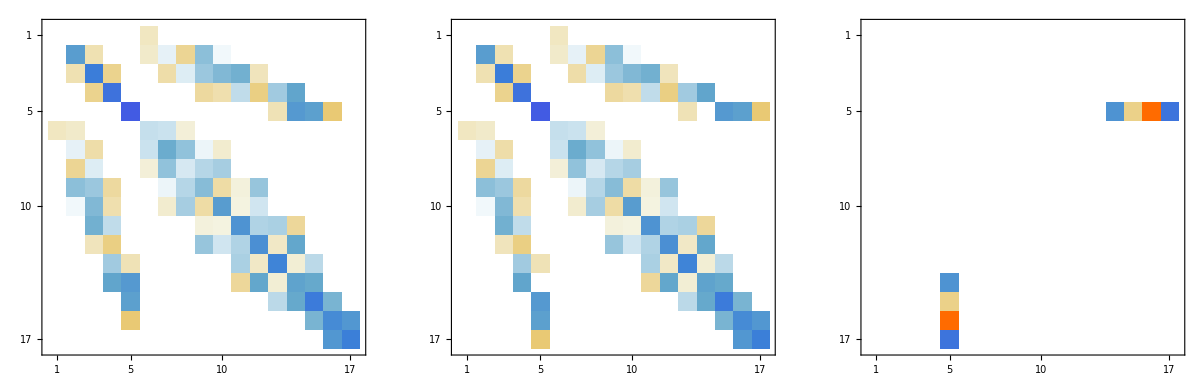
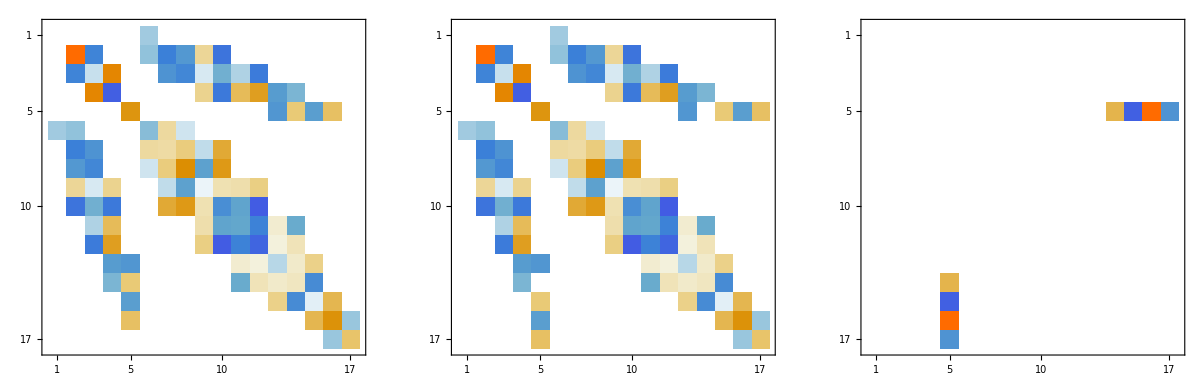
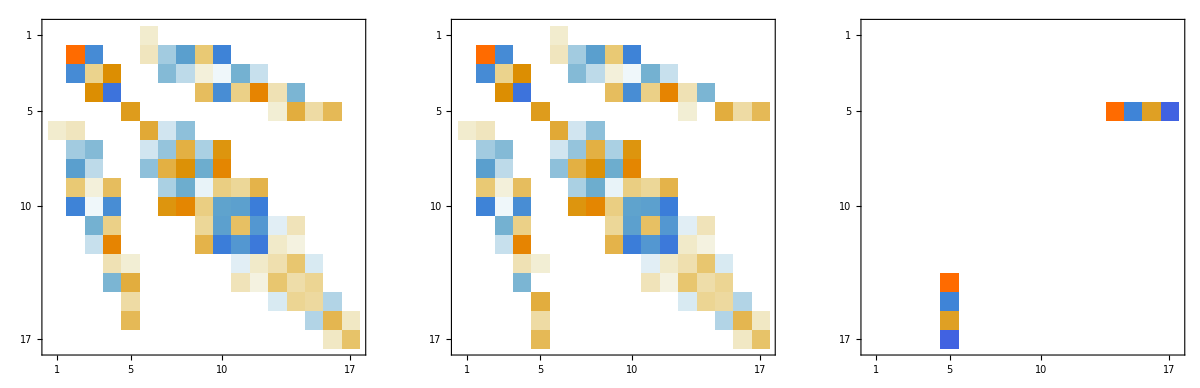
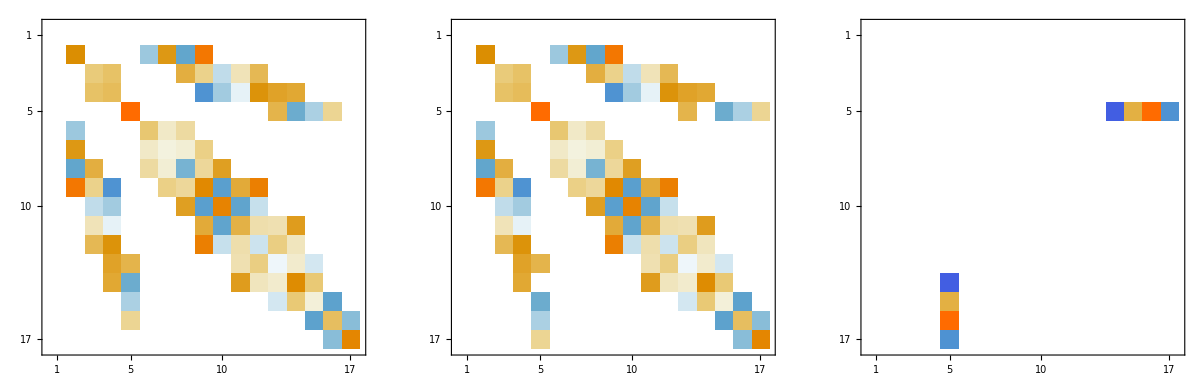
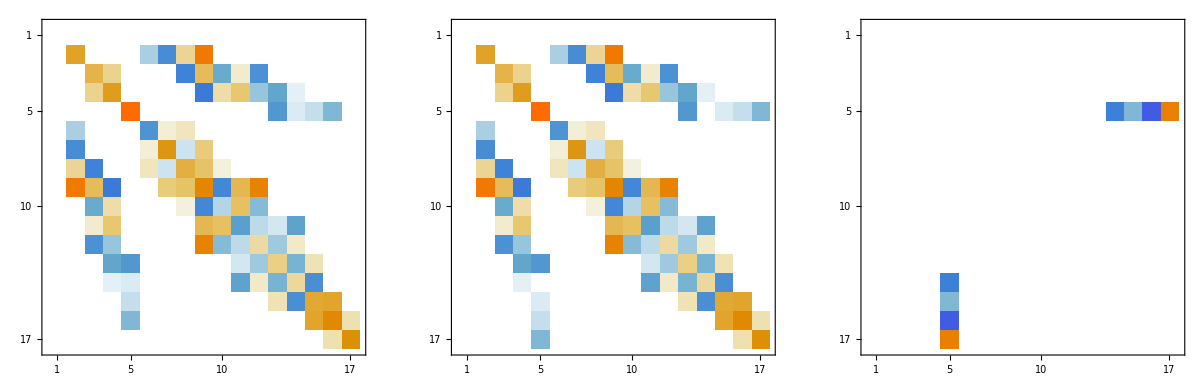
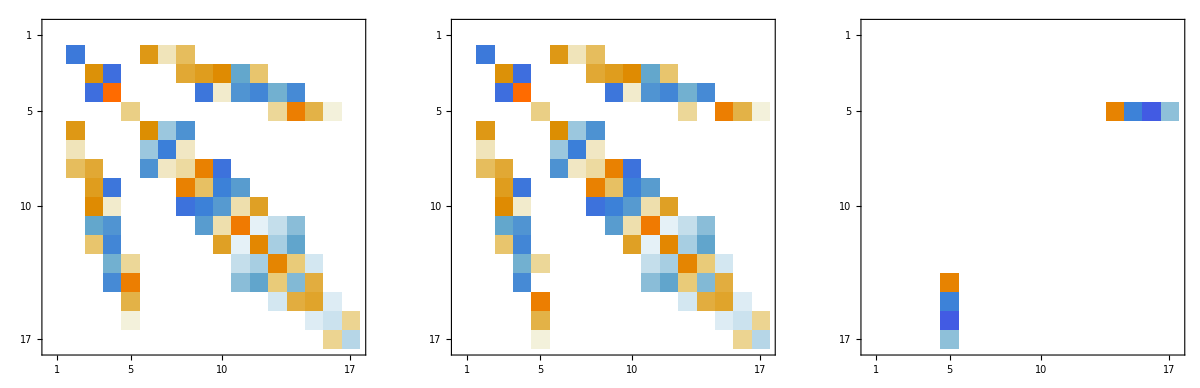
-Graphics-{M0,0.930102}
-Graphics-{M2,0.961892}
-Graphics-{M4,0.988961}
-Graphics-{P2,0.973619}
-Graphics-{P4,0.99575}
-Graphics-{P6,0.957749}

```mathematica
big=Column[rows]
```

```mathematica
Rasterize[big]
```

-Graphics-

```mathematica
plots=Table[(
PrintTemporary[numElectrons];
configTerms=fncross[["terms"]][numElectrons];
matrixReps=<||>;
Do[
(
magElements=fncross[["MKPK"]][op];
magKeys=Keys[magElements];
tab=Table[
(
val=If[MemberQ[magKeys,{numElectrons,braT,ketT}],
magElements[{numElectrons,braT,ketT}],
0
];
If[MemberQ[magKeys,{numElectrons,ketT,braT}],
val=magElements[{numElectrons,ketT,braT}]
];
val
),{braT,configTerms},{ketT,configTerms}];
matrixReps[op]=tab
),
{op,MsAndPs}];
configTerms=fncrossDef[["terms"]][numElectrons];
matrixRepsDef=<||>;
Do[
(
magElements=fncrossDef[["MKPK"]][op];
magKeys=Keys[magElements];
tab=Table[
(
val=If[MemberQ[magKeys,{numElectrons,braT,ketT}],
magElements[{numElectrons,braT,ketT}],
0
];
If[MemberQ[magKeys,{numElectrons,ketT,braT}],
val=magElements[{numElectrons,ketT,braT}]
];
val
),{braT,configTerms},{ketT,configTerms}];
matrixRepsDef[op]=tab
),
{op,MsAndPs}];

rows=Table[(
m1=matrixReps[op];
m2=matrixRepsDef[op];
v1=Flatten[m1];
v2=Flatten[m2];
dist=(v1.v2)/(Sqrt[v1.v1] * Sqrt[v2.v2]);
Labeled[
GraphicsRow[{
MatrixPlot[m1],
MatrixPlot[m2],
MatrixPlot[m1-m2]
}],
{numElectrons,op,dist}
]
),{op,MsAndPs}];
Rasterize[Column[rows]]
)
,{numElectrons,{2,3,5,7}}];
```

```mathematica
Do[(
fname=FileNameJoin[{"~/Desktop","someplots","diff-f"<>{2,3,5,6}[[i]]<>".png"}];
Export[fname,plots[[i]]];
),{i,1,Length[plots]}]
```